# Triangle percolation in d=3 Hyperbolic Lattice

# G. Bianconi and R. M. Ziff

## Generating functions (from Appendix of paper)

```mathematica
Subscript[T, n+1]=p*(x^3*Subscript[T, n][x]^3+9x^2 Subscript[T, n][x]^2*Subscript[S, n][x,x]+3*x^3*Subscript[T, n][x]^2 Subscript[W, n][x,x,x]+24x^3 Subscript[T, n][x]Subscript[S, n][x,x]^2+3*x^2*Subscript[T, n][x]Subscript[S, n][x,1]^2+12x^3 Subscript[T, n][x]*Subscript[S, n][x,x]Subscript[W, n][x,x,x]+6*x^2*Subscript[T, n][x]*Subscript[S, n][x,1]Subscript[W, n][x,x,1]+3x^2 Subscript[T, n][x]*Subscript[W, n][x,x,1]^2+14*x^3*Subscript[S, n][x,x]^3+9x^2 Subscript[S, n][x,x]Subscript[S, n][x,1]^2+Subscript[S, n][1,x]^3+3*x*Subscript[S, n][x,1]^2*Subscript[S, n][1,x]+3 Subscript[S, n][1,x]^2 Subscript[W, n][x,1,1]+6*x*Subscript[S, n][x,1]*Subscript[S, n][1,x]*Subscript[W, n][x,x,1]+12*x^2*Subscript[S, n][x,1]*Subscript[S, n][x,x]*Subscript[W, n][x,x,1]+3*x*Subscript[S, n][x,1]^2*Subscript[W, n][x,1,1]+3*x^2 Subscript[S, n][x,1]^2*Subscript[W, n][x,x,x]+3*Subscript[S, n][1,x]*Subscript[W, n][x,1,1]^2+6*Subscript[S, n][x,1]*Subscript[W, n][x,1,1]*Subscript[W, n][x,x,1]+Subscript[W, n][x,1,1]^3)+(1-p)(x^3*Subscript[T, n][x]^3+6*x^2*Subscript[T, n][x]^2*Subscript[S, n][x,x]+3*x^2*Subscript[T, n][x]*Subscript[S, n][x,1]^2);

Subscript[S, n+1]=(1-p)(x^3*Subscript[T, n][x]^2*Subscript[S, n][x,y]+x^3 Subscript[T, n][x]^2 Subscript[W, n][x,x,y]+4*x^3*Subscript[T, n][x]*Subscript[S, n][x,x]Subscript[S, n][x,y]+2*x^2*y*Subscript[T, n][x]*Subscript[S, n][y,x]Subscript[S, n][x,y]+2*x^2*Subscript[T, n][x]Subscript[S, n][x,1]*Subscript[W, n][x,y,1]+x*y^2*Subscript[T, n][y]Subscript[S, n][x,y]^2+x*Subscript[S, n][x,1]^2 Subscript[S, n][1,y]+2*x*y*Subscript[S, n][x,y]*Subscript[S, n][x,1]*Subscript[S, n][y,1]+x Subscript[S, n][x,1]^2*Subscript[W, n][y,1,1]+x^2 Subscript[S, n][x,1]^2*Subscript[S, n][x,y]);
Subscript[W, n+1]=(1-p)(x^3 Subscript[T, n][x]*Subscript[S, n][x,y]Subscript[S, n][x,z]+x^3 Subscript[T, n][x]Subscript[S, n][x,z]*Subscript[W, n][x,x,y]+x^2*z*Subscript[T, n][x]Subscript[S, n][z,x]*Subscript[W, n][x,y,z]+x^3 Subscript[T, n][x]Subscript[S, n][x,y]*Subscript[W, n][x,x,z]+x^2*y Subscript[T, n][x]Subscript[S, n][y,x]*Subscript[W, n][x,y,z]+x^2 Subscript[T, n][x]*Subscript[W, n][x,y,1]*Subscript[W, n][x,z,1]+z^3 Subscript[T, n][z]*Subscript[S, n][z,x]Subscript[S, n][z,y]+z^3 Subscript[T, n][z]Subscript[S, n][z,x]*Subscript[W, n][y,z,z]+x*z^2*Subscript[T, n][z]Subscript[S, n][x,z]*Subscript[W, n][x,y,z]+z^3 Subscript[T, n][z]*Subscript[S, n][z,y]Subscript[W, n][x,z,z]+y*z^2*Subscript[T, n][z]Subscript[S, n][y,z]*Subscript[W, n][x,y,z]+z^2 Subscript[T, n][z]*Subscript[W, n][x,z,1]*Subscript[W, n][y,z,1]+y^3 Subscript[T, n][y]*Subscript[S, n][y,x]Subscript[S, n][y,z]+y^3 Subscript[T, n][y]Subscript[S, n][y,x]*Subscript[W, n][y,y,z]+x*y^2 Subscript[T, n][y]Subscript[S, n][x,y]*Subscript[W, n][x,y,z]+y^3 Subscript[T, n][y]Subscript[S, n][y,z]*Subscript[W, n][x,y,y]+y^2*z*Subscript[T, n][y]Subscript[S, n][z,y]*Subscript[W, n][x,y,z]+y^2 Subscript[T, n][y]*Subscript[W, n][x,y,1]*Subscript[W, n][y,z,1]+Subscript[S, n][1,x]Subscript[S, n][1,y]Subscript[S, n][1,z]+2*y^3 Subscript[S, n][y,x]Subscript[S, n][y,y]Subscript[S, n][y,z]+Subscript[S, n][1,x]Subscript[S, n][1,z]Subscript[W, n][y,1,1]+z^3 Subscript[S, n][z,x]Subscript[S, n][z,y]Subscript[S, n][z,z]+y*z^2 Subscript[S, n][z,x]Subscript[S, n][z,y]Subscript[S, n][y,z]+z^2 Subscript[S, n][z,x]Subscript[S, n][z,1]Subscript[W, n][y,z,1]+z^3 Subscript[S, n][z,x]Subscript[S, n][z,y]Subscript[S, n][z,z]+y^2*z*Subscript[S, n][y,x]Subscript[S, n][z,y]Subscript[S, n][y,z]+z*Subscript[S, n][1,x]Subscript[S, n][z,1]Subscript[W, n][y,z,1]+Subscript[S, n][1,x]Subscript[S, n][1,y]Subscript[W, n][z,1,1]+y*Subscript[S, n][1,x]Subscript[S, n][y,1]Subscript[W, n][y,z,1]+y^2*Subscript[S, n][y,x]Subscript[S, n][y,1]Subscript[W, n][y,z,1]+Subscript[S, n][1,x]Subscript[W, n][y,1,1]Subscript[W, n][z,1,1]+
x^3 Subscript[S, n][x,x]Subscript[S, n][x,z]Subscript[S, n][x,y]+x^2*y*Subscript[S, n][x,y]Subscript[S, n][y,x]Subscript[S, n][x,z]+x^2*Subscript[S, n][x,1]Subscript[S, n][x,x]Subscript[W, n][x,y,1]+x*z^2*Subscript[S, n][x,z]Subscript[S, n][z,x]Subscript[S, n][z,y]+x*y*z*Subscript[S, n][x,y]Subscript[S, n][z,x]Subscript[S, n][y,z]+x*z*Subscript[S, n][x,1]Subscript[S, n][z,x]Subscript[W, n][y,z,1]+x*Subscript[S, n][x,1]Subscript[S, n][1,y]Subscript[W, n][x,z,1]+x*y*Subscript[S, n][x,1]Subscript[S, n][y,1]Subscript[W, n][x,y,z]+x*y*Subscript[S, n][x,y]Subscript[S, n][y,1]Subscript[W, n][x,z,1]+x*Subscript[S, n][x,1]Subscript[W, n][x,z,1]Subscript[W, n][y,1,1]+x^3 Subscript[S, n][x,x]Subscript[S, n][x,z]Subscript[S, n][x,y]+x*y^2*Subscript[S, n][x,y]Subscript[S, n][y,x]Subscript[S, n][y,z]+x*Subscript[S, n][x,1]Subscript[S, n][1,z]Subscript[W, n][x,y,1]+x^2*z*Subscript[S, n][x,z]Subscript[S, n][x,y]Subscript[S, n][z,x]+x*y*z*Subscript[S, n][x,z]Subscript[S, n][y,x]Subscript[S, n][z,y]+x*z*Subscript[S, n][x,z]Subscript[S, n][z,1]Subscript[W, n][x,y,1]+x*z*Subscript[S, n][x,1]Subscript[S, n][z,1]Subscript[W, n][x,y,z]+x^2*Subscript[S, n][x,1]Subscript[S, n][x,y]Subscript[W, n][x,z,1]+x*y*Subscript[S, n][x,1]Subscript[S, n][y,1]Subscript[W, n][x,y,z]+x*Subscript[S, n][x,1]Subscript[W, n][x,y,1]Subscript[W, n][z,1,1]+
Subscript[S, n][1,y]Subscript[S, n][1,z]Subscript[W, n][x,1,1]+y^2 Subscript[S, n][y,z]Subscript[S, n][y,1]Subscript[W, n][x,y,1]+y*Subscript[S, n][y,1]Subscript[S, n][1,z]Subscript[W, n][x,y,1]+Subscript[S, n][1,z]Subscript[W, n][x,1,1]Subscript[W, n][y,1,1]+z*Subscript[S, n][1,y]*Subscript[S, n][z,1]*Subscript[W, n][x,z,1]+y*z*Subscript[S, n][z,y]*Subscript[S, n][y,1]*Subscript[W, n][x,z,1]+y*z*Subscript[S, n][z,1]*Subscript[S, n][y,1]*Subscript[W, n][x,y,z]+z*Subscript[S, n][z,1]Subscript[W, n][x,z,1]Subscript[W, n][y,1,1]+z^2 Subscript[S, n][z,1]Subscript[S, n][z,y]Subscript[W, n][x,z,1]+y*z*Subscript[S, n][z,1]Subscript[S, n][y,z]Subscript[W, n][x,y,1]+z*Subscript[S, n][z,1]Subscript[W, n][x,1,1]Subscript[W, n][y,z,1]+Subscript[S, n][1,y]Subscript[W, n][x,1,1]Subscript[W, n][z,1,1]+y*Subscript[S, n][y,1]Subscript[W, n][x,1,1]Subscript[W, n][y,z,1]+y*Subscript[S, n][y,1]Subscript[W, n][x,y,1]Subscript[W, n][z,1,1]+Subscript[W, n][x,1,1]Subscript[W, n][y,1,1]Subscript[W, n][z,1,1]);
```

## Derivation of Eqs. (80)

Here we simplified the notation and used 
 T0 for  (T̂)_(n,) 
S0 for (Ŝ)_n
W0 for  (Ŵ)_n
T for T_n(x)
S3 for S_n(x,x)
S2 for S_n(x,1)
S1 for S_n(1,x)
W3 for W_n(x,x,x)
W2 for W_n(x,x,1)
W1 for W_n(x,1,1)

Equation for T [ i.e. T_n(x)]

```mathematica
Subscript[T, n+1]=Subscript[T, n+1]/.Subscript[T, n][x]->T;
Subscript[T, n+1]=Subscript[T, n+1]/.Subscript[T, n][1]->T0;
Subscript[T, n+1]=Subscript[T, n+1]/.Subscript[S, n][x,x]->S3;
Subscript[T, n+1]=Subscript[T, n+1]/.Subscript[S, n][x,1]->S2;
Subscript[T, n+1]=Subscript[T, n+1]/.Subscript[S, n][1,x]->S1;
Subscript[T, n+1]=Subscript[T, n+1]/.Subscript[W, n][x,x,x]->W3;
Subscript[T, n+1]=Subscript[T, n+1]/.Subscript[W, n][x,x,1]->W2;
Subscript[T, n+1]=Subscript[T, n+1]/.Subscript[W, n][x,1,1]->W1;
Subscript[T, n+1]=Factor[Subscript[T, n+1]]
```

p S1^3+3 p S1^2 W1+3 p S1 W1^2+p W1^3+6 p S2 W1 W2+3 p S1 S2^2 x+3 p S2^2 W1 x+6 p S1 S2 W2 x+9 p S2^2 S3 x^2+3 S2^2 T x^2+6 S3 T^2 x^2+3 p S3 T^2 x^2+12 p S2 S3 W2 x^2+6 p S2 T W2 x^2+3 p T W2^2 x^2+3 p S2^2 W3 x^2+14 p S3^3 x^3+24 p S3^2 T x^3+T^3 x^3+12 p S3 T W3 x^3+3 p T^2 W3 x^3

Equations for 
S3 = S_n(x,x)
S2 = S_n(x,1)
S1 = S_n(1,x)

```mathematica
Subscript[S3, n+1]=Subscript[S, n+1]/.y->x;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[T, n][x]->T;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[T, n][1]->T0;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[S, n][x,x]->S3;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[S, n][x,1]->S2;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[S, n][1,x]->S1;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[S, n][1,x]->S0;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[W, n][x,x,x]->W3;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[W, n][x,x,1]->W2;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[W, n][x,1,1]->W1;
Subscript[S3, n+1]=Subscript[S3, n+1]/.Subscript[W, n][1,1,1]->W0;
Subscript[S3, n+1]=Factor[Subscript[S3, n+1]]

Subscript[S2, n+1]=Subscript[S, n+1]/.y->1;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[T, n][x]->T;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[T, n][1]->T0;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[S, n][x,x]->S3;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[S, n][x,1]->S2;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[S, n][1,x]->S1;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[S, n][1,1]->S0;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[W, n][x,x,x]->W3;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[W, n][x,x,1]->W2;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[W, n][x,1,1]->W1;
Subscript[S2, n+1]=Subscript[S2, n+1]/.Subscript[W, n][1,1,1]->W0;
Subscript[S2, n+1]=Factor[Subscript[S2, n+1]]

Subscript[S1, n+1]=Subscript[S, n+1]/.x->1;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[T, n][y]->T;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[T, n][1]->T0;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[S, n][y,y]->S3;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[S, n][y,1]->S2;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[S, n][1,y]->S1;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[S, n][1,1]->S0;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[W, n][y,y,y]->W3;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[W, n][y,y,1]->W2;Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[W, n][1,y,y]->W3;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[W, n][y,1,y]->W2;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[W, n][y,1,1]->W1;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[W, n][1,y,1]->W1;
Subscript[S1, n+1]=Subscript[S1, n+1]/.Subscript[W, n][1,1,y]->W1;
Subscript[S1, n+1]=Subscript[S1, n+1]/.y->x;
Subscript[S1, n+1]=Factor[Subscript[S1, n+1]]
```

-(-1+p) x (S1 S2^2+S2^2 W1+3 S2^2 S3 x+2 S2 T W2 x+7 S3^2 T x^2+S3 T^2 x^2+T^2 W3 x^2)

-(-1+p) x (3 S0 S2^2+S2^2 T0+S2^2 W0+S2^3 x+2 S1 S2 T x+2 S2 T W1 x+4 S2 S3 T x^2+S2 T^2 x^2+T^2 W2 x^2)

-(-1+p) (2 S0^2 S1+4 S0 S1 T0+S1 T0^2+S0^2 W1+2 S0 T0 W1+T0^2 W1+2 S0 S1 S2 x+2 S1 S2 T0 x+S1^2 T x^2)

Equations for 
W3 = W_n(x,x,x)
W2 = W_n(x,x,1)
W1 =W_n(x,1,1)

```mathematica
Subscript[W3, n+1]=Subscript[W, n+1]/.y->x;
Subscript[W3, n+1]=Subscript[W3, n+1]/.z->x;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[T, n][x]->T;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[T, n][1]->T0;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[S, n][x,x]->S3;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[S, n][x,1]->S2;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[S, n][1,x]->S1;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[S, n][1,1]->S0;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[W, n][x,x,x]->W3;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[W, n][x,x,1]->W2;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[W, n][x,1,1]->W1;
Subscript[W3, n+1]=Subscript[W3, n+1]/.Subscript[W, n][1,1,1]->W0;
Subscript[W3, n+1]=Factor[Subscript[W3, n+1]];


Subscript[W2, n+1]=Subscript[W, n+1]/.y->x;
Subscript[W2, n+1]=Subscript[W2, n+1]/.z->1;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[T, n][x]->T;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[T, n][1]->T0;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[S, n][x,x]->S3;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[S, n][x,1]->S2;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[S, n][1,x]->S1;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[S, n][1,1]->S0;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[W, n][x,x,x]->W3;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[W, n][x,x,1]->W2;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[W, n][x,1,1]->W1;
Subscript[W2, n+1]=Subscript[W2, n+1]/.Subscript[W, n][1,1,1]->W0;
Subscript[W2, n+1]=Factor[Subscript[W2, n+1]];


Subscript[W1, n+1]=Subscript[W, n+1]/.y->1;
Subscript[W1, n+1]=Subscript[W1, n+1]/.z->1;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[T, n][x]->T;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[T, n][1]->T0;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[S, n][x,x]->S3;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[S, n][x,1]->S2;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[S, n][1,x]->S1;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[S, n][1,1]->S0;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[W, n][x,x,x]->W3;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[W, n][x,x,1]->W2;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[W, n][x,1,1]->W1;
Subscript[W1, n+1]=Subscript[W1, n+1]/.Subscript[W, n][1,1,1]->W0;
Subscript[W1, n+1]=Factor[Subscript[W2, n+1]];
```

Determination of the vectorial function F in Eq. (45)

```mathematica
V={T,S3,S2,S1,W3,W2,W1};
Subscript[V, n+1]={T->Subscript[T, n+1],S3->Subscript[S3, n+1], S2->Subscript[S2, n+1],S1->Subscript[S1, n+1], W3->Subscript[W3, n+1],W2->Subscript[W2, n+1], W1->Subscript[W1, n+1]};
F=V/. Subscript[V, n+1];
```

Double check: Reduction of the above equations to Eqs. (34) for x = 1

```mathematica
MatrixForm[Factor[Subscript[V, n+1]/.T0->T/.S3->S/.S2->S/.S1->S/.S0->S/.W3->W/.W2->W/.W1->W/.W0->W/.W->(1-T-3*S)/.x->1]]
```

(T→p+3 S^2 T-3 p S^2 T+6 S T^2-6 p S T^2+T^3-p T^3
S→-(-1+p) (S^2+S^3+2 S T+T^2-4 S T^2-T^3)
S→-(-1+p) (S^2+S^3+2 S T+T^2-4 S T^2-T^3)
S→-(-1+p) (S^2+S^3+2 S T+T^2-4 S T^2-T^3)
1-3 S-T→(-1+p) (-1+3 S^2+3 S^3+6 S T+3 S^2 T+3 T^2-6 S T^2-2 T^3)
1-3 S-T→(-1+p) (-1+3 S^2+3 S^3+6 S T+3 S^2 T+3 T^2-6 S T^2-2 T^3)
1-3 S-T→(-1+p) (-1+3 S^2+3 S^3+6 S T+3 S^2 T+3 T^2-6 S T^2-2 T^3))

### Second check: T + 3 S + W = 1

```mathematica
FullSimplify[(F[[1]]+3F[[2]]+F[[5]])/.T0->T/.S3->S/.S2->S/.S1->S/.S0->S/.W3->W/.W2->W/.W1->W/.W0->W/.x->1/.W->(1-T-3S)]
```

1

## Derivation of Eq. (46):

### We first derive the non - linear term of Eq. (46)

```mathematica
MatrixForm[dFdx=D[F,x]]
```

(3 p S1 S2^2+3 p S2^2 W1+6 p S1 S2 W2+18 p S2^2 S3 x+6 S2^2 T x+12 S3 T^2 x+6 p S3 T^2 x+24 p S2 S3 W2 x+12 p S2 T W2 x+6 p T W2^2 x+6 p S2^2 W3 x+42 p S3^3 x^2+72 p S3^2 T x^2+3 T^3 x^2+36 p S3 T W3 x^2+9 p T^2 W3 x^2
-(-1+p) x (3 S2^2 S3+2 S2 T W2+14 S3^2 T x+2 S3 T^2 x+2 T^2 W3 x)-(-1+p) (S1 S2^2+S2^2 W1+3 S2^2 S3 x+2 S2 T W2 x+7 S3^2 T x^2+S3 T^2 x^2+T^2 W3 x^2)
-(-1+p) x (S2^3+2 S1 S2 T+2 S2 T W1+8 S2 S3 T x+2 S2 T^2 x+2 T^2 W2 x)-(-1+p) (3 S0 S2^2+S2^2 T0+S2^2 W0+S2^3 x+2 S1 S2 T x+2 S2 T W1 x+4 S2 S3 T x^2+S2 T^2 x^2+T^2 W2 x^2)
-(-1+p) (2 S0 S1 S2+2 S1 S2 T0+2 S1^2 T x)
-(-1+p) (6 S1 S2 W2+6 S2 W1 W2+22 S2 S3 W2 x+6 T W2^2 x+8 S2^2 W3 x+42 S3^3 x^2+9 S3^2 T x^2+36 S3 T W3 x^2)
-(-1+p) (2 S1^2 S2+4 S1 S2 W1+2 S2 W1^2+6 S0 S2 W2+2 S2 T0 W2+2 S2 W0 W2+8 S1 S2 S3 x+6 S2 S3 W1 x+6 S2^2 W2 x+2 S2 S3 W2 x+4 S1 T W2 x+4 T W1 W2 x+18 S2 S3^2 x^2+6 S2 S3 T x^2+12 S3 T W2 x^2+6 S2 T W3 x^2)
-(-1+p) (2 S1^2 S2+4 S1 S2 W1+2 S2 W1^2+6 S0 S2 W2+2 S2 T0 W2+2 S2 W0 W2+8 S1 S2 S3 x+6 S2 S3 W1 x+6 S2^2 W2 x+2 S2 S3 W2 x+4 S1 T W2 x+4 T W1 W2 x+18 S2 S3^2 x^2+6 S2 S3 T x^2+12 S3 T W2 x^2+6 S2 T W3 x^2))

### We then derive the explicit expression of the Jacobian J of the vectorial function F given by Eq. (48)

```mathematica
MatrixForm[dFdV=D[F,{{T,S3,S2,S1,W3,W2,W1}}]]
```

(3 S2^2 x^2+12 S3 T x^2+6 p S3 T x^2+6 p S2 W2 x^2+3 p W2^2 x^2+24 p S3^2 x^3+3 T^2 x^3+12 p S3 W3 x^3+6 p T W3 x^3 | 9 p S2^2 x^2+6 T^2 x^2+3 p T^2 x^2+12 p S2 W2 x^2+42 p S3^2 x^3+48 p S3 T x^3+12 p T W3 x^3 | 6 p W1 W2+6 p S1 S2 x+6 p S2 W1 x+6 p S1 W2 x+18 p S2 S3 x^2+6 S2 T x^2+12 p S3 W2 x^2+6 p T W2 x^2+6 p S2 W3 x^2 | 3 p S1^2+6 p S1 W1+3 p W1^2+3 p S2^2 x+6 p S2 W2 x | 3 p S2^2 x^2+12 p S3 T x^3+3 p T^2 x^3 | 6 p S2 W1+6 p S1 S2 x+12 p S2 S3 x^2+6 p S2 T x^2+6 p T W2 x^2 | 3 p S1^2+6 p S1 W1+3 p W1^2+6 p S2 W2+3 p S2^2 x
-(-1+p) x (2 S2 W2 x+7 S3^2 x^2+2 S3 T x^2+2 T W3 x^2) | -(-1+p) x (3 S2^2 x+14 S3 T x^2+T^2 x^2) | -(-1+p) x (2 S1 S2+2 S2 W1+6 S2 S3 x+2 T W2 x) | -(-1+p) S2^2 x | -(-1+p) T^2 x^3 | -2 (-1+p) S2 T x^2 | -(-1+p) S2^2 x
-(-1+p) x (2 S1 S2 x+2 S2 W1 x+4 S2 S3 x^2+2 S2 T x^2+2 T W2 x^2) | -4 (-1+p) S2 T x^3 | -(-1+p) x (6 S0 S2+2 S2 T0+2 S2 W0+3 S2^2 x+2 S1 T x+2 T W1 x+4 S3 T x^2+T^2 x^2) | -2 (-1+p) S2 T x^2 | 0 | -(-1+p) T^2 x^3 | -2 (-1+p) S2 T x^2
-(-1+p) S1^2 x^2 | 0 | -(-1+p) (2 S0 S1 x+2 S1 T0 x) | -(-1+p) (2 S0^2+4 S0 T0+T0^2+2 S0 S2 x+2 S2 T0 x+2 S1 T x^2) | 0 | 0 | -(-1+p) (S0^2+2 S0 T0+T0^2)
-(-1+p) (3 W2^2 x^2+3 S3^2 x^3+12 S3 W3 x^3) | -(-1+p) (11 S2 W2 x^2+42 S3^2 x^3+6 S3 T x^3+12 T W3 x^3) | -(-1+p) (6 S1 W2 x+6 W1 W2 x+11 S3 W2 x^2+8 S2 W3 x^2) | -(-1+p) (3 S1^2+6 S1 W1+3 W1^2+6 S2 W2 x) | -(-1+p) (4 S2^2 x^2+12 S3 T x^3) | -(-1+p) (6 S1 S2 x+6 S2 W1 x+11 S2 S3 x^2+6 T W2 x^2) | -(-1+p) (3 S1^2+6 S1 W1+3 W1^2+6 S2 W2 x)
-(-1+p) (2 S1 W2 x^2+2 W1 W2 x^2+2 S2 S3 x^3+4 S3 W2 x^3+2 S2 W3 x^3) | -(-1+p) (4 S1 S2 x^2+3 S2 W1 x^2+S2 W2 x^2+12 S2 S3 x^3+2 S2 T x^3+4 T W2 x^3) | -(-1+p) (2 S1^2 x+4 S1 W1 x+2 W1^2 x+6 S0 W2 x+2 T0 W2 x+2 W0 W2 x+4 S1 S3 x^2+3 S3 W1 x^2+6 S2 W2 x^2+S3 W2 x^2+6 S3^2 x^3+2 S3 T x^3+2 T W3 x^3) | -(-1+p) (6 S0 S1+2 S1 T0+2 S1 W0+6 S0 W1+2 T0 W1+2 W0 W1+4 S1 S2 x+4 S2 W1 x+4 S2 S3 x^2+2 T W2 x^2) | -2 (-1+p) S2 T x^3 | -(-1+p) (6 S0 S2 x+2 S2 T0 x+2 S2 W0 x+3 S2^2 x^2+S2 S3 x^2+2 S1 T x^2+2 T W1 x^2+4 S3 T x^3) | -(-1+p) (6 S0 S1+2 S1 T0+2 S1 W0+6 S0 W1+2 T0 W1+2 W0 W1+4 S1 S2 x+4 S2 W1 x+3 S2 S3 x^2+2 T W2 x^2)
-(-1+p) (2 S1 W2 x^2+2 W1 W2 x^2+2 S2 S3 x^3+4 S3 W2 x^3+2 S2 W3 x^3) | -(-1+p) (4 S1 S2 x^2+3 S2 W1 x^2+S2 W2 x^2+12 S2 S3 x^3+2 S2 T x^3+4 T W2 x^3) | -(-1+p) (2 S1^2 x+4 S1 W1 x+2 W1^2 x+6 S0 W2 x+2 T0 W2 x+2 W0 W2 x+4 S1 S3 x^2+3 S3 W1 x^2+6 S2 W2 x^2+S3 W2 x^2+6 S3^2 x^3+2 S3 T x^3+2 T W3 x^3) | -(-1+p) (6 S0 S1+2 S1 T0+2 S1 W0+6 S0 W1+2 T0 W1+2 W0 W1+4 S1 S2 x+4 S2 W1 x+4 S2 S3 x^2+2 T W2 x^2) | -2 (-1+p) S2 T x^3 | -(-1+p) (6 S0 S2 x+2 S2 T0 x+2 S2 W0 x+3 S2^2 x^2+S2 S3 x^2+2 S1 T x^2+2 T W1 x^2+4 S3 T x^3) | -(-1+p) (6 S0 S1+2 S1 T0+2 S1 W0+6 S0 W1+2 T0 W1+2 W0 W1+4 S1 S2 x+4 S2 W1 x+3 S2 S3 x^2+2 T W2 x^2))

### We evaluate the above two expressions for x = 1

```mathematica
Subscript[DFV, n_]:=Factor[(dFdV/.x->1/.S3->S/.S2->S/.S1->S/.W3->1-T-3*S/.W2->(1-T-3*S)/.W1->(1-T-3S))/.W2->(1-T-3S)/.W3->(1-T-3S)/.W0->(1-T-3*S)/.T0->T/.S0->S/.T->Subscript[T, n]/.S->Subscript[S, n]]
Subscript[DFx, n_]:=Factor[(dFdx/.x->1/.S3->S/.S2->S/.S1->S/.W3->1-T-3*S/.W2->(1-T-3*S)/.W1->(1-T-3S))/.W2->(1-T-3S)/.W3->(1-T-3S)/.W0->(1-T-3*S)/.T0->T/.S0->S/.T->Subscript[T, n]/.S->Subscript[S, n]]

Simplify[Subscript[DFV, n]]
Simplify[Subscript[DFx, n]]
```

{{-3 (-p+(-1+p) S_n^2+4 (-1+p) S_n T_n+(-1+p) T_n^2),3 (4 p S_n+5 p S_n^2+T_n (4 p+(2-3 p) T_n)),-6 (2 p S_n^2+p (-1+T_n)+S_n (p+(-1+2 p) T_n)),-3 p (S_n^2-2 S_n (-1+T_n)-(-1+T_n)^2),3 p (S_n^2+4 S_n T_n+T_n^2),-6 p ((-1+T_n) T_n+S_n (-1+3 T_n)),-3 p (S_n^2-2 S_n (-1+T_n)-(-1+T_n)^2)},{-(-1+p) (S_n^2+S_n (2-6 T_n)-2 (-1+T_n) T_n),-(-1+p) (3 S_n^2+14 S_n T_n+T_n^2),-2 (-1+p) (S_n+S_n^2+T_n-4 S_n T_n-T_n^2),-(-1+p) S_n^2,-(-1+p) T_n^2,-2 (-1+p) S_n T_n,-(-1+p) S_n^2},{2 (-1+p) ((-1+T_n) T_n+S_n (-1+3 T_n)),-4 (-1+p) S_n T_n,-(-1+p) (2 S_n+3 S_n^2-(-2+T_n) T_n),-2 (-1+p) S_n T_n,0,-(-1+p) T_n^2,-2 (-1+p) S_n T_n},{-(-1+p) S_n^2,0,-2 (-1+p) S_n (S_n+T_n),-(-1+p) (4 S_n^2+8 S_n T_n+T_n^2),0,0,-(-1+p) (S_n+T_n)^2},{3 (-1+p) (2 S_n^2-2 S_n (-1+T_n)-(-1+T_n)^2),-(-1+p) (9 S_n^2+S_n (11-41 T_n)-12 (-1+T_n) T_n),(-1+p) (6+7 S_n-6 T_n) (-1+3 S_n+T_n),3 (-1+p) (2 S_n^2-2 S_n (-1+T_n)-(-1+T_n)^2),-4 (-1+p) S_n (S_n+3 T_n),(-1+p) (S_n^2+6 (-1+T_n) T_n+6 S_n (-1+4 T_n)),3 (-1+p) (2 S_n^2-2 S_n (-1+T_n)-(-1+T_n)^2)},{2 (-1+p) (2 S_n^2-2 S_n (-1+T_n)-(-1+T_n)^2),-2 (-1+p) (2 S_n^2+S_n (2-7 T_n)-2 (-1+T_n) T_n),2 (-1+p) (6 S_n^2+2 (-1+T_n)+S_n (2+3 T_n)),2 (-1+p) (-1+2 S_n^2+5 S_n T_n+T_n^2),-2 (-1+p) S_n T_n,-2 (-1+p) (S_n+2 S_n^2+T_n-T_n^2),(-1+p) (-2+5 S_n^2+10 S_n T_n+2 T_n^2)},{2 (-1+p) (2 S_n^2-2 S_n (-1+T_n)-(-1+T_n)^2),-2 (-1+p) (2 S_n^2+S_n (2-7 T_n)-2 (-1+T_n) T_n),2 (-1+p) (6 S_n^2+2 (-1+T_n)+S_n (2+3 T_n)),2 (-1+p) (-1+2 S_n^2+5 S_n T_n+T_n^2),-2 (-1+p) S_n T_n,-2 (-1+p) (S_n+2 S_n^2+T_n-T_n^2),(-1+p) (-2+5 S_n^2+10 S_n T_n+2 T_n^2)}}

{-3 (18 p S_n^3+S_n T_n (-4 p+(-4+11 p) T_n)+S_n^2 (-13 p+(-2+19 p) T_n)+T_n (-2 p+p T_n+(-1+p) T_n^2)),-(-1+p) (4 S_n^3+2 S_n (2-5 T_n) T_n-3 (-1+T_n) T_n^2+S_n^2 (1+8 T_n)),-(-1+p) (2 S_n^3+2 S_n (2-5 T_n) T_n-3 (-1+T_n) T_n^2+S_n^2 (1+4 T_n)),-2 (-1+p) S_n^2 (S_n+2 T_n),3 (-1+p) (4 S_n^3-2 S_n (-1+T_n)^2+15 S_n^2 T_n-2 (-1+T_n)^2 T_n),2 (-1+p) (4 S_n^3-2 S_n (-1+T_n)^2+15 S_n^2 T_n-2 (-1+T_n)^2 T_n),2 (-1+p) (4 S_n^3-2 S_n (-1+T_n)^2+15 S_n^2 T_n-2 (-1+T_n)^2 T_n)}

## Eigenvalue of the Jacobian Matrix in Eq. (48) for p>p_2^u

### The Jacobian J of the vectorial function F given by Eq. (48) calculated at x=1 is given for p>p_2^u by

```mathematica
MatrixForm[Subscript[DFV, n]/.Subscript[T, n]->1/.Subscript[S, n]->0/.T0->1/.S0->0]
```

(3 | 3 (2+p) | 0 | 0 | 3 p | 0 | 0
0 | 1-p | 0 | 0 | 1-p | 0 | 0
0 | 0 | 1-p | 0 | 0 | 1-p | 0
0 | 0 | 0 | 1-p | 0 | 0 | 1-p
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

### With eigenvalues

```mathematica
Eigenvalues[%]
```

{3,0,0,0,1-p,1-p,1-p}

The maximum eigenvalue λ=3 yields  a fractal exponent ψ=1 above the upper percolation threshold p_2^u

## Discontinuity

Here we determine the discontinuity at p_2^u by imposing Eqs. (36) together with Eq. (37).
In particular we observe that the maximum eigenvalue Λ_G=1 of the Jacobian J_G of G  is equal to one, (i.e. Λ_G=1) if and  only if Det[I-J_G]=0 (where I indicates the identity matrix).

We first find Det[I-J_G]

```mathematica
Clear[p];
K={T,S,W};
Subscript[K, n+1]={T->Subscript[T, n+1],S->Subscript[S3, n+1], W0->Subscript[W1, n+1]};
R=FullSimplify[K/. Subscript[K, n+1]/.T0->T/.S3->S/.S2->S/.S1->S/.S0->S/.W3->W/.W2->W/.W1->W/.W0->W/.W->(1-T-3*S)/.x->1]
MatrixForm[dRdK=D[K-R,{{T,S,W}}]/.x->1]
Det[dRdK]
```

{p-3 (-1+p) S^2 T-6 (-1+p) S T^2-(-1+p) T^3,-(-1+p) (S^2+S^3+2 S (1-2 T) T-(-1+T) T^2),1-3 S-T}

(1+3 (-1+p) S^2+12 (-1+p) S T+3 (-1+p) T^2 | 6 (-1+p) S T+6 (-1+p) T^2 | 0
(-1+p) (2 S (1-2 T)-4 S T-2 (-1+T) T-T^2) | 1+(-1+p) (2 S+3 S^2+2 (1-2 T) T) | 0
1 | 3 | 1)

-(-1+p) (2 S (1-2 T)-4 S T-2 (-1+T) T-T^2) (6 (-1+p) S T+6 (-1+p) T^2)+(1+3 (-1+p) S^2+12 (-1+p) S T+3 (-1+p) T^2) (1+(-1+p) (2 S+3 S^2+2 (1-2 T) T))

### We then solve Eqs.(36) together with Det[I-J_G]=0

```mathematica
transition=FindRoot[{T==p-3 (-1+p) S^2 T-6 (-1+p) S T^2-(-1+p) T^3,S==-(-1+p) (S^2+S^3+2 S (1-2 T) T-(-1+T) T^2),(1+3 (-1+p) S^2+12 (-1+p) S T+3 (-1+p) T^2)(1+(-1+p) (2 S+3 S^2+2 (1-2 T) T))-(6 (-1+p) S T+6 (-1+p) T^2)((-1+p) (2 S (1-2 T)-4 S T-2 (-1+T) T-T^2))==0},{p,0.37},{T,0.55},{S,0.001}]
```

{p→0.307981,T→0.509801,S→0.0934843}

## Numerical Solution

### We numerically evaluate (T̂)_n(indicate here as T[n]) as a function of p up to n=NI (here choosen ot be NI=25) and we plot the numerical result

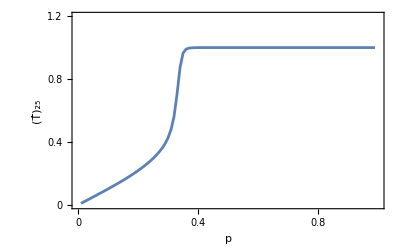

```mathematica
NI=25;
HT=Table[{p=i*0.01;
T[0]=p;
S[0]=0;Vprime={0,0,0,0,0,0,0};
n=-1;
W[n+1]=1−3 S[n+1]−T[n+1];
For[n=0,n<NI,n++,T[n+1]=p+(1−p) (T[n]^3+6 T[n]^2 S[n]+3 T[n] S[n]^2);
S[n+1]=(1−p) (T[n]^2 (S[n]+W[n])+T[n] S[n] (7 S[n]+2 W[n])+S[n]^2 (4 S[n]+W[n]));
W[n+1]=1−3 S[n+1]−T[n+1];]};
{p,T[NI]},{i,1,99}];
ListPlot[{HT},Joined->True,PlotRange->{{0,1},{0,1.2}},FrameLabel->{Style["p",Bold,20],Style[Subscript[OverHat[T], NI],Bold,20]
},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1,1.2},None},{{0,0.2,0.4,0.6,0.8,1,1.2},None}},LabelStyle->Directive[Bold,15],Frame->True,PlotStyle->{Thickness[0.005],Dashed,DotDashed}]
```

### We numerically evaluate the fractal critical exponent ψ_n as a function of p [calculated using (T̂)_n(indicate here as T[n])] for n=NI (here choosen to be NI=100) and we plot the numerical result.

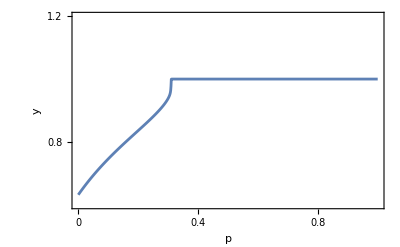

```mathematica
NI=100;
Psi=Table[{p=i*0.001;
T[0]=p;
S[0]=0;Vprime={0,0,0,0,0,0,0};
n=-1;
W[n+1]=1−3 S[n+1]−T[n+1];
For[n=0,n<NI,n++,T[n+1]=p+(1−p) (T[n]^3+6 T[n]^2 S[n]+3 T[n] S[n]^2);
S[n+1]=(1−p) (T[n]^2 (S[n]+W[n])+T[n] S[n] (7 S[n]+2 W[n])+S[n]^2 (4 S[n]+W[n]));
W[n+1]=1−3 S[n+1]−T[n+1];];ev=Eigenvalues[FullSimplify[Subscript[DFV, n]/.Subscript[T, n]->T[NI]/.Subscript[S, n]->S[NI]]];};
{p,Log[ev[[1]]]/Log[3]},{i,1,999}];
ListPlot[{Psi},Joined->True,PlotRange->{{0,1},{0.6,1.2}},FrameLabel->{Style["p",Bold,20],Style["y",Bold,20]
},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1,1.2},None},{{0,0.2,0.4,0.6,0.8,1,1.2},None}},LabelStyle->Directive[Bold,15],Frame->True,PlotStyle->{Thickness[0.005]}]
```

### We numerically evaluate the order parameter M_n as a function of p [calculated using (T̂)_n(indicate here as T[n])] for n=NI (here choosen to be NI=25) and we plot the numerical result.

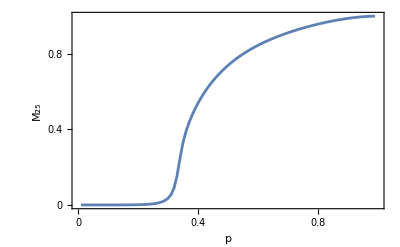

```mathematica
Clear[n,p];NI=25;
pc=p;
PT=Table[{p=i*0.01;
T[0]=p;
S[0]=0;Vprime={0,0,0,0,0,0,0};
n=-1;
W[n+1]=1−3 S[n+1]−T[n+1];
For[n=0,n<NI,n++,T[n+1]=p+(1−p) (T[n]^3+6 T[n]^2 S[n]+3 T[n] S[n]^2);
S[n+1]=(1−p) (T[n]^2 (S[n]+W[n])+T[n] S[n] (7 S[n]+2 W[n])+S[n]^2 (4 S[n]+W[n]));
W[n+1]=1−3 S[n+1]−T[n+1];Vprime=(Subscript[DFV, n].Vprime+Subscript[DFx, n])/.Subscript[T, n]->T[n]/.Subscript[S, n]->S[n]/.Subscript[W, n]->W[n];]};
{p,Vprime[[1]]/(1.5+3^(NI+1)*0.5)},{i,1,99}];
ListPlot[{PT},Joined->True,PlotRange->{{0,1},{0,1}},FrameLabel->{Style["p",Bold,20],Style[Subscript["M", NI],Bold,20]
},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1,1.2},None},{{0,0.2,0.4,0.6,0.8,1,1.2},None}},LabelStyle->Directive[Bold,15],Frame->True,PlotStyle->{Thickness[0.005]}]
```

We numerically evaluate the critical behavior of M_n as a function of p 
[calculated using  (T̂)_n(indicate here as T[n])]  for  n=NI  (here choosen to be NI=300)
and we plot the numerical result.

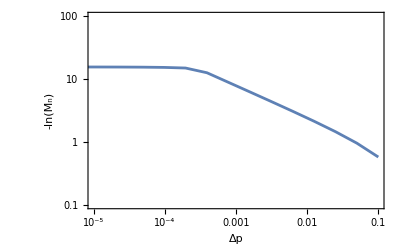

```mathematica
NI=300;
pc=0.30798093163606444;
M=Table[{p=(pc+0.2*2^(-i));
T[0]=p;
S[0]=0;Vprime={0,0,0,0,0,0,0};
n=-1;
W[n+1]=1−3 S[n+1]−T[n+1];
For[n=0,n<NI,n++,T[n+1]=p+(1−p) (T[n]^3+6 T[n]^2 S[n]+3 T[n] S[n]^2);
S[n+1]=(1−p) (T[n]^2 (S[n]+W[n])+T[n] S[n] (7 S[n]+2 W[n])+S[n]^2 (4 S[n]+W[n]));
W[n+1]=1−3 S[n+1]−T[n+1];Vprime=(Subscript[DFV, n].Vprime+Subscript[DFx, n])/.Subscript[T, n]->T[n]/.Subscript[S, n]->S[n]/.Subscript[W, n]->W[n];]};
{p-pc,-Log[Vprime[[1]]/(1.5+3^(NI+1)*0.5)]},{i,1,18}];

ListLogLogPlot[{M},Joined->True,FrameLabel->{Style["Δp",Bold,20],Style["-ln(M_n)",Bold,20]},Frame->True,PlotStyle->{Thickness[0.005]},PlotRange->{{10^(-5),0.1},{0.1,100}},LabelStyle->Directive[Bold,15]]
```